```mathematica
(*BISEKCJA*)
bisekcja[f_,a_,b_,ϵ_] :=Module[{c,a1,b1,z=1},
c= (a+b)/2.; a1=a; b1=b;
While[Abs[f[c]] > ϵ,
If[f[a1]*f[c] < 0, b1=c,a1=c];
c=(a1+b1)/2;
z++];
Print["Pierwiastkiem równania ",f[x],"=0 \njest liczba ",c," uzyskana po zrobieniu ",z," połowień" ] 
]

(*PROGRAM TESTOWY*)

ft[x_] :=(x+Cos[x])*E^(-Sin[x-ArcTan[1-x x]]);
```

```mathematica
bisekcja[ft,-2,1,.001]
```

Pierwiastkiem równania ⅇ^(-Sin[x-ArcTan[1-x^2]]) (x+Cos[x])=0 
jest liczba -0.739136 uzyskana po zrobieniu 13 połowień

```mathematica
ft1[x_] :=2x-Log[Sin[2x-3]+3E^x]ArcTan[2x+Cos[3x]] -1;
```

```mathematica
bisekcja[ft1,2,6,.001]
```

Pierwiastkiem równania -1+2 x-ArcTan[2 x+Cos[3 x]] Log[3 ⅇ^x-Sin[3-2 x]]=0 
jest liczba 4.86328 uzyskana po zrobieniu 10 połowień

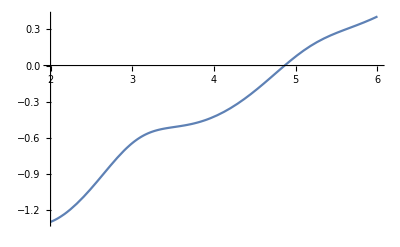

```mathematica
Plot[ft1[x],{x,2,6}]
```

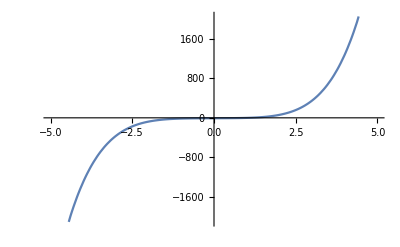

```mathematica
(*ZADANIE A*)

f[x_]:= x^5+4x^3+2x-8
Plot[f[x],{x,-5,5}]
```

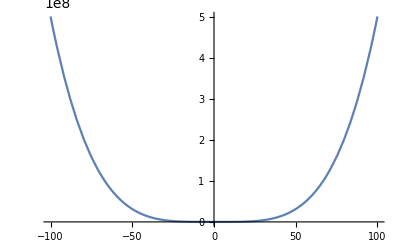

```mathematica
Plot[f'[x],{x,-100,100}]
```

```mathematica
(*Funkcja jest monotoniczna i tylko raz przecina oś OX*)
bisekcja[f,-5,5,.001]
```

Pierwiastkiem równania -8+2 x+4 x^3+x^5=0 
jest liczba 1.04965 uzyskana po zrobieniu 16 połowień

```mathematica
(*ZADANIE B*)
g[x_]:=Exp[-x^2]*Sin[x]-Cos[x]
```

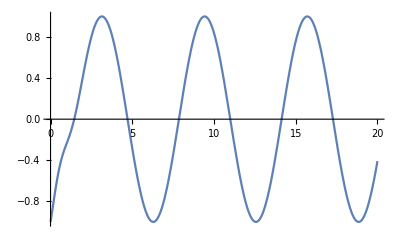

```mathematica
Plot[g[x],{x,0,20}]
```

```mathematica
bisekcja[g,1,2,10^-6]
```

Pierwiastkiem równania -Cos[x]+ⅇ^(-x^2) Sin[x]=0 
jest liczba 1.44884 uzyskana po zrobieniu 17 połowień

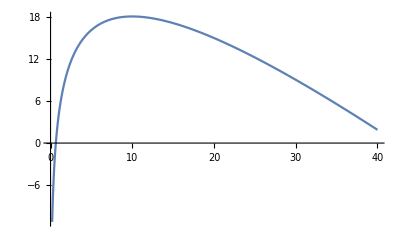

```mathematica
(*ZADANIE C*)

(*10ln(x)+5≤x -> 10ln(x)+5-x≤0*)
h[x_]:= 10Log[x]+5-x
Plot[h[x],{x,0,40}]
```

```mathematica
bisekcja[h,0,2,10^-6]
```

Pierwiastkiem równania 5-x+10 Log[x]=0 
jest liczba 0.647075 uzyskana po zrobieniu 23 połowień